```mathematica
FindB4CReductionLength[g_]:=Block[{Candidates=BarelyFourColorableGraphsOfCount[VertexCount[g]], edgeCount=EdgeCount[g], difference,new},
Select[
Flatten[
Table[
difference=EdgeCount[can]-EdgeCount[g];
If[difference==0 ,
If[IsomorphicGraphQ[can,g],
0, Null]
,
Table[
new=EdgeAdd[g,s];
If[IsomorphicGraphQ[can,new],
Length[s],
Null
]
,{s,Subsets[EdgeList[GraphComplement[g]],{difference}]}
]
]
,{can,Candidates}
]

],
#=!=Null&
]
]
```

```mathematica
FindB4CReduction[g_]:=Block[{
Candidates=BarelyFourColorableGraphsOfCount[VertexCount[g]], 
edgeCount=EdgeCount[g], 
difference,
new,
iso,
can2
},
Select[
Flatten[
Table[
difference=EdgeCount[can]-EdgeCount[g];
If[difference==0 ,
If[IsomorphicGraphQ[can,g],
{}<->BeautiGraph[can], Null]
,
Table[
new=EdgeAdd[g,s];
If[IsomorphicGraphQ[can,new],
iso=First[FindGraphIsomorphism [can,new]];
can2=EdgeList[can]/.Normal[iso];
Graph[BeautiGraph[Graph[can2]],EdgeStyle->Map[#->{Darker[Green],Thick}&,s],ImageSize->200],
Null
]
,{s,Subsets[EdgeList[GraphComplement[g]],{difference}]}
]
]
,{can,Candidates}
]

],
#=!=Null&
]
]
```

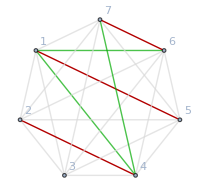

```mathematica
FindB4CReduction[ReadGrof[5]]
```

```mathematica
FindFullFormula4[ReadGrof[19]]
```

{v14x28x35x67,v18x24x35x67,v16x28x35x47,v15x28x34x67}

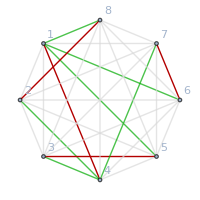
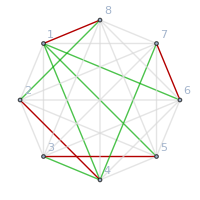
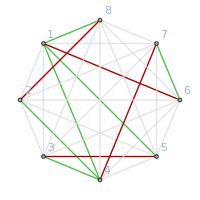
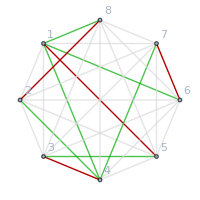

```mathematica
FindB4CReduction[ReadGrof[19]]
```

```mathematica
FindFullFormula4[ReadGrof[20]]
```

{v14x25x37x68,v16x248x37x5,v16x25x3x478,v16x25x37x48}

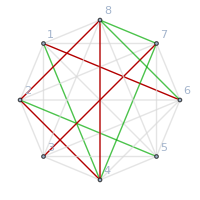
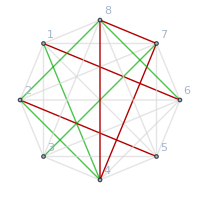
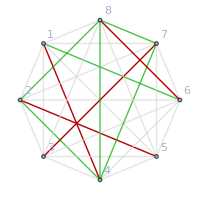
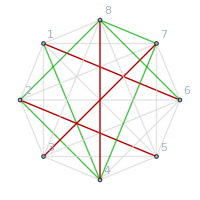

```mathematica
FindB4CReduction[ReadGrof[20]]
```

```mathematica
FindFullFormula4[ReadGrof[21]]
```

{v1x267x35x48,v16x24x35x78,v16x27x35x48,v14x26x35x78,v14x267x35x8,v148x2x35x67,v148x26x35x7,v18x24x35x67,v148x267x3x5,v18x267x35x4,v148x27x35x6}

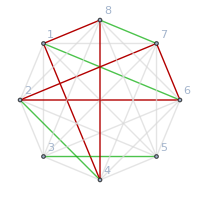
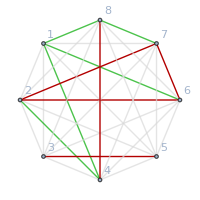
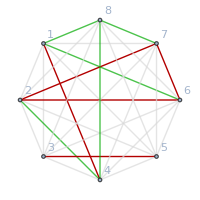
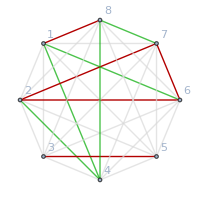
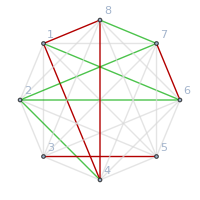
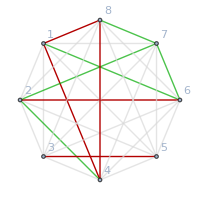
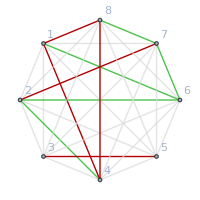
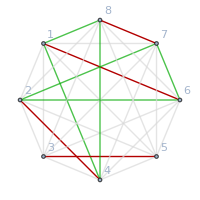

```mathematica
FindB4CReduction[ReadGrof[21]]
```

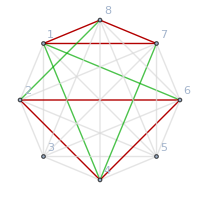

```mathematica
FindB4CReduction[ReadGrof[22]]
```

```mathematica
Table[ChromaticPolynomial[ReadGrof[k],4]/24 <->k,{k,40}]//Sort
```

{1<->1,1<->2,1<->3,1<->5,1<->8,1<->9,1<->10,1<->12,1<->13,1<->16,1<->17,1<->22,1<->23,1<->24,1<->27,1<->28,1<->29,1<->32,1<->33,1<->34,3<->18,3<->36,3<->38,4<->4,4<->6,4<->14,4<->15,4<->19,4<->20,4<->25,4<->30,4<->35,5<->7,5<->11,5<->26,5<->31,5<->39,9<->40,12<->21,12<->37}

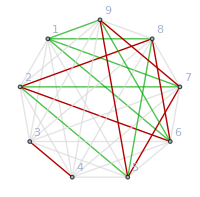
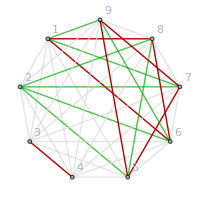
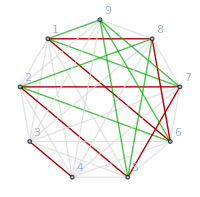
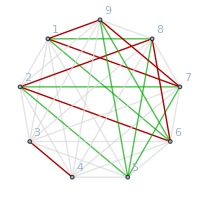
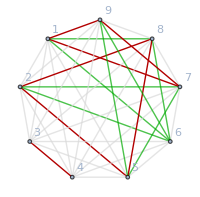
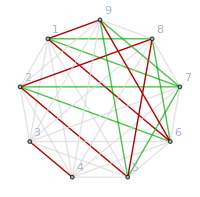
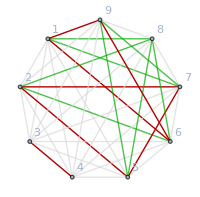
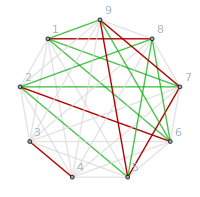

```mathematica
FindB4CReduction[JacobsThalGraph[5]]
```

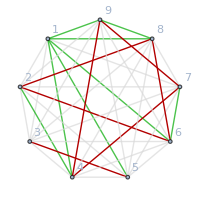
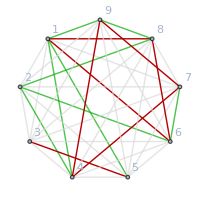
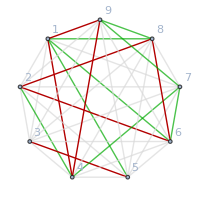
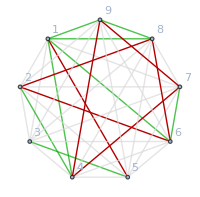
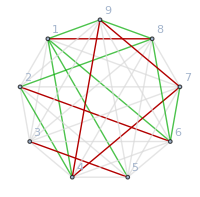
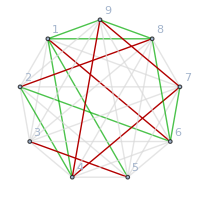
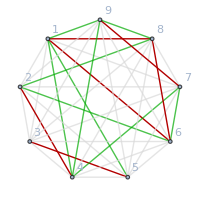
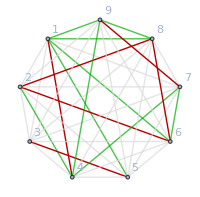

```mathematica
FindB4CReduction[ReadGrof[37]]
```

```mathematica
EdgeList[ReadGrof[36]]
```

{1<->2,1<->3,1<->7,2<->3,2<->6,2<->7,2<->9,3<->5,3<->6,3<->7,3<->8,4<->5,4<->6,4<->8,4<->9,5<->7,5<->8,5<->9,6<->8,6<->9,7<->9}

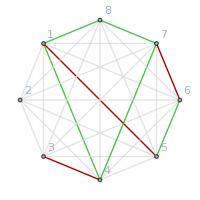
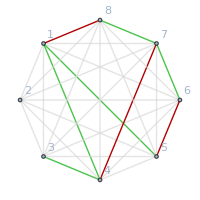
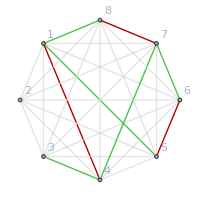
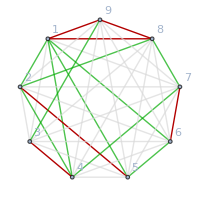
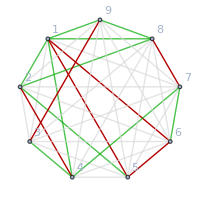
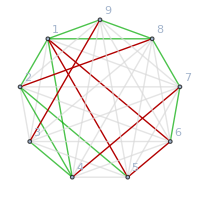
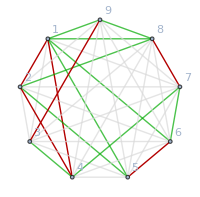
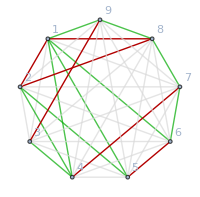

```mathematica
{FindB4CReduction[EdgeContract[ReadGrof[36],1<->2]],FindB4CReduction[EdgeDelete[ReadGrof[36],1<->2]]}
```

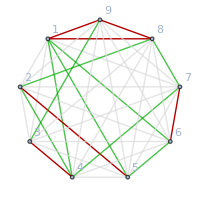
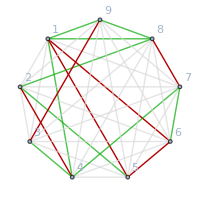
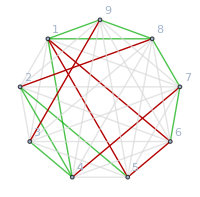

```mathematica
FindB4CReduction[ReadGrof[36]]
```

```mathematica
FindB4CReductionLength[ReadGrof[5]]
```

{3}

```mathematica
FindB4CReductionLength[ReadGrof[36]]
```

{9,9,9}

```mathematica
Monitor[Table[k->FindB4CReductionLength[ReadGrof[k]],{k,80}],k]
```

{1→{0},2→{0},3→{1},4→{1,1,1},5→{3},6→{3,3,3,3},7→{3,3,3,3,3},8→{2},9→{3},10→{6},11→{5,5,6,6,6},12→{5},13→{5},14→{5,5,5,6},15→{5,6,6,6},16→{5},17→{6},18→{6,6,6},19→{6,6,6,6},20→{5,5,6,6},21→{4,5,5,5,5,5,5,6,6,6,6},22→{4},23→{6},24→{9},25→{9,9,9,9},26→{8,8,9,9,9},27→{9},28→{9},29→{9},30→{8,8,9,9},31→{9,9,9,9,9},32→{9},33→{9},34→{9},35→{9,9,9,9},36→{9,9,9},37→{8,8,8,8,9,9,9,9,9,9,9,9},38→{9,9,9},39→{8,9,9,9,9},40→{8,8,8,8,9,9,9,9,9},41→{8,8,9,9,9,9},42→{8,9,9,9,9},43→{9,9,9,9,9},44→{8,9,9,9,9},45→{7,7,9,9,9},46→{9,9},47→{8},48→{8},49→{8,9,9,9},50→{8},51→{7},52→{9},53→{8},54→{8},55→{7},56→{8,8,9,9},57→{8,9,9,9},58→{9},59→{8},60→{8},61→{9},62→{8,8,8,8,8,8,8,8,8,9,9,9,9,9,9},63→{8,8,9,9},64→{8,8,9,9},65→{7,9,9,9},66→{9,9,9,9},67→{9,9,9,9},68→{8},69→{9},70→{9},71→{8},72→{8,8,8,8,8,8,8,9,9,9,9,9,9,9,9,9,9,9,9,9,9},73→{6},74→{13},75→{13},76→{12,13,13,13,13},77→{12},78→{12,13,13,13},79→{13,13,13,13},80→{12,12,13,13,13,13,13,13,13,13,13,13}}

```mathematica
Map[{Max[#[[2]]]-Min[#[[2]]],Min[#[[2]]],Max[#[[2]]]}->#[[1]]&,%]//Sort
```

{{0,0,0}→1,{0,0,0}→2,{0,1,1}→3,{0,1,1}→4,{0,2,2}→8,{0,3,3}→5,{0,3,3}→6,{0,3,3}→7,{0,3,3}→9,{0,4,4}→22,{0,5,5}→12,{0,5,5}→13,{0,5,5}→16,{0,6,6}→10,{0,6,6}→17,{0,6,6}→18,{0,6,6}→19,{0,6,6}→23,{0,6,6}→73,{0,7,7}→51,{0,7,7}→55,{0,8,8}→47,{0,8,8}→48,{0,8,8}→50,{0,8,8}→53,{0,8,8}→54,{0,8,8}→59,{0,8,8}→60,{0,8,8}→68,{0,8,8}→71,{0,9,9}→24,{0,9,9}→25,{0,9,9}→27,{0,9,9}→28,{0,9,9}→29,{0,9,9}→31,{0,9,9}→32,{0,9,9}→33,{0,9,9}→34,{0,9,9}→35,{0,9,9}→36,{0,9,9}→38,{0,9,9}→43,{0,9,9}→46,{0,9,9}→52,{0,9,9}→58,{0,9,9}→61,{0,9,9}→66,{0,9,9}→67,{0,9,9}→69,{0,9,9}→70,{0,12,12}→77,{0,13,13}→74,{0,13,13}→75,{0,13,13}→79,{1,5,6}→11,{1,5,6}→14,{1,5,6}→15,{1,5,6}→20,{1,8,9}→26,{1,8,9}→30,{1,8,9}→37,{1,8,9}→39,{1,8,9}→40,{1,8,9}→41,{1,8,9}→42,{1,8,9}→44,{1,8,9}→49,{1,8,9}→56,{1,8,9}→57,{1,8,9}→62,{1,8,9}→63,{1,8,9}→64,{1,8,9}→72,{1,12,13}→76,{1,12,13}→78,{1,12,13}→80,{2,4,6}→21,{2,7,9}→45,{2,7,9}→65}